# Mathematica as a Tool for Astronomy and Physics

## Lecture 3 Wintersemester 2009/10 Markus Röllig

## Application Example: Astrochemical Reactions

Astrochemistry deals with the formation/destruction of chemical species under interstellar medium conditions. A standard database of gas phase reactions is the so called UMIST database for astrochemistry. Two different versions of this database will be compared in this example.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Markus Röllig\Documents\Projekte\Teaching\Vorlesung\Mathematica\WS2009-10

```mathematica
umist=Import["umist06.csv","CSV"];
umist95=Import["umist95.csv","CSV"];
```

```mathematica
umist[[1;;3]]
```

{{1,NN,H,CH,,C,H2,,,1.31×10^-10,0.,80.,C,300,2000,B,NIST},{2,NN,H,CH2,,CH,H2,,,6.64×10^-11,0.,0.,L,300,2500,A,NIST},{3,NN,H,NH,,N,H2,,,1.73×10^-11,0.5,2400.,L,80,300,C,}}

```mathematica
umist95[[1;;3]]
```

{{1,H      ,H2     ,H      ,H     ,H  ,  ,4.7×10^-7,-1.,55000.,CD},{2,H      ,C      ,CH     ,PHOTON,   ,  ,1.×10^-17,0.,0.,NA},{3,H      ,CH     ,C      ,H2    ,   ,  ,5.×10^-11,0.,0.,NE}}

Lists of all chemical species

```mathematica
listSpecies=umist[[All,{3,4,6,7,8,9}]]
```

{{H,CH,C,H2,,},{H,CH2,CH,H2,,},{H,NH,N,H2,,},{H,CH3,CH2,H2,,},{H,NH2,NH,H2,,},{H,NH2,NH,H2,,},«4587»,{O,O,O2,M,,},{O,NO,NO2,M,,},{O,SO,SO2,M,,},{OH,OH,H2O2,M,,},{O2H,O2H,H2O2,O2,M,}}

```mathematica
listSpecies=Flatten@umist[[All,{3,4,6,7,8,9}]]
```

{H,CH,C,H2,,,H,CH2,CH,H2,,,H,NH,N,H2,,,H,CH3,CH2,H2,,,H,NH2,NH,H2,,,H,NH2,NH,H2,,,«27516»,CH3,OH,CH3OH,M,,,O,O,O2,M,,,O,NO,NO2,M,,,O,SO,SO2,M,,,OH,OH,H2O2,M,,,O2H,O2H,H2O2,O2,M,}

```mathematica
listSpecies=Union@Flatten@umist[[All,{3,4,6,7,8,9}]]
```

{,C,C-,C+,C10,C10+,C2,C2+,C2H,C2H+,C2H2,C2H2+,C2H3,C2H3+,C2H3CN+,C2H4,C2H4+,C2H5,C2H5+,C2H5OH,C2H5OH+,C2H5OH2+,C2H7+,C2N,C2N+,C2N2+,C2NH+,C2O,C2O+,C2S,C2S+,C3,C3+,C3H,C3H+,C3H2,C3H2+,C3H2O+,C3H3,C3H3+,C3H5+,C3H6+,C3H7+,C3N,C3N+,C3O,C3O+,C3P,C3S,C3S+,C4,C4+,C4H,C4H+,C4H2+,C4H3,C4H3+,C4H4+,C4H5+,C4H7+,C4N,C4N+,C4P,C4P+,C4S,C4S+,C5,C5+,C5H,C5H+,C5H2,C5H2+,C5H3+,C5H5+,C5N,C5N+,C6,C6+,C6H,C6H+,C6H2,C6H2+,C6H3+,C6H4+,C6H5+,C6H6,C6H6+,C6H7+,C7,C7+,C7H,C7H+,C7H2,C7H2+,C7H3+,C7H4,C7H4+,C7H5+,C7N,C7N+,C8,C8+,C8H,C8H+,C8H2,C8H2+,C8H3+,C8H4+,C8H5+,C9,C9+,C9H,C9H+,C9H2,C9H2+,C9H3+,C9H4+,C9H5+,C9N,C9N+,CCl,CCl+,CCP,CCP+,CF+,CH,CH+,CH2,CH2+,CH2CHCN,CH2CN,CH2CN+,CH2CO+,CH2NH,CH2NH2+,CH2PH,CH3,CH3+,CH3C3N,CH3C3N+,CH3C3NH+,CH3C4H,CH3C4H+,CH3C5N,CH3C5NH+,CH3C7N,CH3C7NH+,CH3CCH,CH3CCH+,CH3CH3,CH3CH3+,CH3CHO,CH3CHO+,CH3CHOH+,CH3CN,CH3CN+,CH3CNH+,CH3CO+,CH3COCH3,CH3COCH3+,CH3COCH4+,CH3CS+,CH3OCH3,CH3OCH3+,CH3OCH4+,CH3OH,CH3OH+,CH3OH2+,CH4,CH4+,CH4N+,CH5+,Cl,Cl+,ClO,ClO+,CN,CN-,CN+,CNC+,CO,CO+,CO2,CO2+,COOCH4+,CP,CP+,CRP,CRPHOT,CS,CS+,e-,F,F+,Fe,Fe+,H,H-,H+,H2,H2+,H2C3H+,H2C4N+,H2C5N+,H2C7N+,H2C9N+,H2CCC,H2CCCC,H2CCl+,H2CCO,H2Cl+,H2CN,H2CO,H2CO+,H2CS,H2CS+,H2F+,H2NC+,H2NO+,H2O,H2O+,H2O2,H2PO+,H2S,H2S+,H2S2,H2S2+,H2SiO,H2SiO+,H3+,H3C3O+,H3C5N+,H3C7N+,H3C9N+,H3CO+,H3CS+,H3O+,H3S+,H3S2+,H3SiO+,H4C3N+,H5C2O2+,HC2O+,HC2P,HC2P+,HC2S+,HC3N,HC3N+,HC3NH+,HC3O+,HC3S+,HC4N+,HC4S+,HC5N,HC5N+,HC7N,HC7N+,HC9N,HC9N+,HCl,HCl+,HCN,HCN+,HCNH+,HCO,HCO+,HCO2+,HCOOCH3,HCOOH,HCOOH+,HCOOH2+,HCP,HCP+,HCS,HCS+,HCSi,HCSi+,He,He+,HeH+,HF,HF+,HN2+,HN2O+,HNC,HNCO+,HNO,HNO+,HNS+,HNSi,HNSi+,HOC+,HOCH,HOCS+,HPN+,HPO,HPO+,HS,HS+,HS2,HS2+,HSiO2+,HSiS+,HSO+,HSO2+,M,Mg,Mg+,N,N+,N2,N2+,N2O,N2O+,Na,Na+,NCCN,NCCNCH3+,NCCNH+,NH,NH+,NH2,NH2+,NH2CN,NH2CNH+,NH3,NH3+,NH4+,NO,NO+,NO2,NO2+,NS,NS+,O,O-,O+,O2,O2+,O2H,O2H+,OCN,OCN+,OCS,OCS+,OH,OH-,OH+,P,P+,PC2H2+,PC2H3+,PC2H4+,PC3H+,PC4H+,PCH2+,PCH3+,PCH4+,PH,PH+,PH2,PH2+,PH3+,PHOTON,PN,PN+,PNH2+,PNH3+,PO,PO+,S,S-,S+,S2,S2+,Si,Si+,SiC,SiC+,SiC2,SiC2+,SiC2H,SiC2H+,SiC2H2,SiC2H2+,SiC2H3+,SiC3,SiC3+,SiC3H,SiC3H+,SiC3H2+,SiC4,SiC4+,SiC4H+,SiCH2,SiCH2+,SiCH3,SiCH3+,SiCH4+,SiF+,SiH,SiH+,SiH2,SiH2+,SiH3,SiH3+,SiH4,SiH4+,SiH5+,SiN,SiN+,SiNC,SiNC+,SiNCH+,SiNH2+,SiO,SiO+,SiO2,SiOH+,SiS,SiS+,SO,SO+,SO2,SO2+}

```mathematica
listSpecies=Rest@Union@Flatten@umist[[All,{3,4,6,7,8,9}]]
```

{C,C-,C+,C10,C10+,C2,C2+,C2H,C2H+,C2H2,C2H2+,C2H3,C2H3+,C2H3CN+,C2H4,C2H4+,C2H5,C2H5+,C2H5OH,C2H5OH+,C2H5OH2+,C2H7+,C2N,C2N+,C2N2+,C2NH+,C2O,C2O+,C2S,C2S+,C3,C3+,C3H,C3H+,C3H2,C3H2+,C3H2O+,C3H3,C3H3+,C3H5+,C3H6+,C3H7+,C3N,C3N+,C3O,C3O+,C3P,C3S,C3S+,C4,C4+,C4H,C4H+,C4H2+,C4H3,C4H3+,C4H4+,C4H5+,C4H7+,C4N,C4N+,C4P,C4P+,C4S,C4S+,C5,C5+,C5H,C5H+,C5H2,C5H2+,C5H3+,C5H5+,C5N,C5N+,C6,C6+,C6H,C6H+,C6H2,C6H2+,C6H3+,C6H4+,C6H5+,C6H6,C6H6+,C6H7+,C7,C7+,C7H,C7H+,C7H2,C7H2+,C7H3+,C7H4,C7H4+,C7H5+,C7N,C7N+,C8,C8+,C8H,C8H+,C8H2,C8H2+,C8H3+,C8H4+,C8H5+,C9,C9+,C9H,C9H+,C9H2,C9H2+,C9H3+,C9H4+,C9H5+,C9N,C9N+,CCl,CCl+,CCP,CCP+,CF+,CH,CH+,CH2,CH2+,CH2CHCN,CH2CN,CH2CN+,CH2CO+,CH2NH,CH2NH2+,CH2PH,CH3,CH3+,CH3C3N,CH3C3N+,CH3C3NH+,CH3C4H,CH3C4H+,CH3C5N,CH3C5NH+,CH3C7N,CH3C7NH+,CH3CCH,CH3CCH+,CH3CH3,CH3CH3+,CH3CHO,CH3CHO+,CH3CHOH+,CH3CN,CH3CN+,CH3CNH+,CH3CO+,CH3COCH3,CH3COCH3+,CH3COCH4+,CH3CS+,CH3OCH3,CH3OCH3+,CH3OCH4+,CH3OH,CH3OH+,CH3OH2+,CH4,CH4+,CH4N+,CH5+,Cl,Cl+,ClO,ClO+,CN,CN-,CN+,CNC+,CO,CO+,CO2,CO2+,COOCH4+,CP,CP+,CRP,CRPHOT,CS,CS+,e-,F,F+,Fe,Fe+,H,H-,H+,H2,H2+,H2C3H+,H2C4N+,H2C5N+,H2C7N+,H2C9N+,H2CCC,H2CCCC,H2CCl+,H2CCO,H2Cl+,H2CN,H2CO,H2CO+,H2CS,H2CS+,H2F+,H2NC+,H2NO+,H2O,H2O+,H2O2,H2PO+,H2S,H2S+,H2S2,H2S2+,H2SiO,H2SiO+,H3+,H3C3O+,H3C5N+,H3C7N+,H3C9N+,H3CO+,H3CS+,H3O+,H3S+,H3S2+,H3SiO+,H4C3N+,H5C2O2+,HC2O+,HC2P,HC2P+,HC2S+,HC3N,HC3N+,HC3NH+,HC3O+,HC3S+,HC4N+,HC4S+,HC5N,HC5N+,HC7N,HC7N+,HC9N,HC9N+,HCl,HCl+,HCN,HCN+,HCNH+,HCO,HCO+,HCO2+,HCOOCH3,HCOOH,HCOOH+,HCOOH2+,HCP,HCP+,HCS,HCS+,HCSi,HCSi+,He,He+,HeH+,HF,HF+,HN2+,HN2O+,HNC,HNCO+,HNO,HNO+,HNS+,HNSi,HNSi+,HOC+,HOCH,HOCS+,HPN+,HPO,HPO+,HS,HS+,HS2,HS2+,HSiO2+,HSiS+,HSO+,HSO2+,M,Mg,Mg+,N,N+,N2,N2+,N2O,N2O+,Na,Na+,NCCN,NCCNCH3+,NCCNH+,NH,NH+,NH2,NH2+,NH2CN,NH2CNH+,NH3,NH3+,NH4+,NO,NO+,NO2,NO2+,NS,NS+,O,O-,O+,O2,O2+,O2H,O2H+,OCN,OCN+,OCS,OCS+,OH,OH-,OH+,P,P+,PC2H2+,PC2H3+,PC2H4+,PC3H+,PC4H+,PCH2+,PCH3+,PCH4+,PH,PH+,PH2,PH2+,PH3+,PHOTON,PN,PN+,PNH2+,PNH3+,PO,PO+,S,S-,S+,S2,S2+,Si,Si+,SiC,SiC+,SiC2,SiC2+,SiC2H,SiC2H+,SiC2H2,SiC2H2+,SiC2H3+,SiC3,SiC3+,SiC3H,SiC3H+,SiC3H2+,SiC4,SiC4+,SiC4H+,SiCH2,SiCH2+,SiCH3,SiCH3+,SiCH4+,SiF+,SiH,SiH+,SiH2,SiH2+,SiH3,SiH3+,SiH4,SiH4+,SiH5+,SiN,SiN+,SiNC,SiNC+,SiNCH+,SiNH2+,SiO,SiO+,SiO2,SiOH+,SiS,SiS+,SO,SO+,SO2,SO2+}

```mathematica
listSpecies95=Rest@Union@Flatten@umist95[[All,2;;7]];
```

This list looks different. What is different?

```mathematica
listSpecies95
```

{   ,C     ,C-     ,C+     ,C      ,C10+   ,C2    ,C2+    ,C2     ,C2H   ,C2H+   ,C2H    ,C2H2  ,C2H2+  ,C2H2   ,C2H3  ,C2H3+  ,C2H3   ,C2H4  ,C2H4+  ,C2H4   ,C2H5  ,C2H5+  ,C2H5   ,C2H5O+ ,C2H5OH+,C2H5OH ,C2H6  ,C2H6+  ,C2H6   ,C2H6CO+,C2H6CO ,C2H6O+ ,C2H6OH+,C2H7+  ,C2H7O+ ,C2HO+  ,C2N2+  ,C2O+   ,C2S+   ,C2S    ,C3    ,C3+    ,C3     ,C3H   ,C3H+   ,C3H    ,C3H2+  ,C3H2   ,C3H2O+ ,C3H3  ,C3H3+  ,C3H3   ,C3H4+  ,C3H4   ,C3H5+  ,C3H6OH+,C3N   ,C3N+   ,C3N    ,C3O   ,C3O+   ,C3O    ,C3P    ,C3S+   ,C3S    ,C4    ,C4+    ,C4     ,C4H   ,C4H+   ,C4H    ,C4H2  ,C4H2+  ,C4H2   ,C4H3+  ,C4H5+  ,C4N+   ,C4P+   ,C4P    ,C4S+   ,C4S    ,C5    ,C5+    ,C5     ,C5H   ,C5H+   ,C5H    ,C5H2  ,C5H2+  ,C5H2   ,C5H3+  ,C5H4+  ,C5H4   ,C5H5+  ,C5N   ,C5N+   ,C5N    ,C6    ,C6+    ,C6     ,C6H   ,C6H+   ,C6H    ,C6H2  ,C6H2+  ,C6H2   ,C6H3+  ,C6H4+  ,C6H5+  ,C7    ,C7+    ,C7     ,C7H   ,C7H+   ,C7H    ,C7H2  ,C7H2+  ,C7H2   ,C7H3+  ,C7H4+  ,C7H4   ,C7H5+  ,C7N   ,C7N+   ,C7N    ,C8    ,C8+    ,C8     ,C8H   ,C8H+   ,C8H    ,C8H2  ,C8H2+  ,C8H2   ,C8H3+  ,C8H4+  ,C8H5+  ,C9+    ,C9     ,C9H+   ,C9H    ,C9H2+  ,C9H2   ,C9H3+  ,C9H4+  ,C9H5+  ,C9N+   ,C9N    ,CCL+   ,CCL    ,CCN+   ,CCN    ,CCNH+  ,CCO   ,CCO    ,CCP   ,CCP+   ,CCP    ,CH    ,CH+    ,CH     ,CH2   ,CH2+   ,CH2    ,CH2CN ,CH2CN+ ,CH2CN  ,CH2CO+ ,CH2CO  ,CH2NH  ,CH2NH2+,CH2PH  ,CH3   ,CH3+   ,CH3    ,CH3CHO,CH3CHO+,CH3CHO ,CH3CN+ ,CH3CN  ,CH3CO+ ,CH3OCH3,CH3OH ,CH3OH+ ,CH3OH  ,CH3OH2+,CH4   ,CH4+   ,CH4    ,CH4N+  ,CH5+   ,CHOOH  ,CHOOH2+,CL    ,CL+    ,CL     ,CLO   ,CLO+   ,CLO    ,CN    ,CN-    ,CN+    ,CN     ,CNC+   ,CO ,CO    ,CO+    ,CO     ,CO2   ,CO2+   ,CO2    ,COOCH4+,CP    ,CP+    ,CP     ,CRP    ,CRPHOT ,CS    ,CS+    ,CS     ,ELECTR,ELECTR ,FE    ,FE+    ,FE     ,H ,H  ,H-    ,H+    ,H     ,H-     ,H+     ,H      ,H2 ,H2    ,H2+    ,H2     ,H2C3  ,H2C3   ,H2C3H+ ,H2C3N+ ,H2C4N+ ,H2C5N+ ,H2C7N+ ,H2C9N+ ,H2CCL+ ,H2CL+  ,H2CN   ,H2CO  ,H2CO+  ,H2CO   ,H2CS  ,H2CS+  ,H2CS   ,H2NC+  ,H2NO+  ,H2O   ,H2O+   ,H2O    ,H2O2   ,H2PO+  ,H2S   ,H2S+   ,H2S    ,H2S2+  ,H2S2   ,H2SIO+ ,H2SIO  ,H3+    ,H3C3N  ,H3C3O+ ,H3C4N+ ,H3C4N  ,H3C5N+ ,H3C6N  ,H3C7N+ ,H3C8N  ,H3C9N+ ,H3CO+  ,H3CS+  ,H3O+   ,H3S+   ,H3S2+  ,H3SIO+ ,H4C2N+ ,H4C3N+ ,H4C4N+ ,H4C6N+ ,H4C8N+ ,H5C2O+ ,H5C2O2+,HC2O+  ,HC2S+  ,HC3N  ,HC3N+  ,HC3N   ,HC3O+  ,HC3S+  ,HC4N+  ,HC4S+  ,HC5N  ,HC5N+  ,HC5N   ,HC7N  ,HC7N+  ,HC7N   ,HC9N+  ,HC9N   ,HCCP   ,HCL   ,HCL+   ,HCL    ,HCN   ,HCN+   ,HCN    ,HCNH+  ,HCO   ,HCO+   ,HCO    ,HCO2+  ,HCOOCH3,HCP+   ,HCP    ,HCS+   ,HCS    ,HCSI+  ,HCSI   ,HE,HE ,HE    ,HE+    ,HE     ,HEH+   ,HNC   ,HNC    ,HNCO+  ,HNO   ,HNO+   ,HNO    ,HNS+   ,HNSI+  ,HNSI   ,HOC+   ,HOCS+  ,HPN+   ,HPO+   ,HPO    ,HS    ,HS+    ,HS     ,HS2    ,HSIO2+ ,HSIS+  ,HSO+   ,HSO2+  ,MG    ,MG+    ,MG     ,N  ,N     ,N+     ,N      ,N2 ,N2    ,N2+    ,N2     ,N2H+   ,N2O    ,NA+    ,NA     ,NCO+   ,NH    ,NH+    ,NH     ,NH2   ,NH2+   ,NH2    ,NH3   ,NH3+   ,NH3    ,NH4+   ,NO    ,NO+    ,NO     ,NO2+   ,NO2    ,NS    ,NS+    ,NS     ,O  ,O+    ,O     ,O-     ,O+     ,O      ,O2    ,O2+    ,O2     ,O2H   ,O2H+   ,O2H    ,OCN    ,OCS+   ,OCS    ,OH ,OH    ,OH-    ,OH+    ,OH     ,P     ,P+     ,P      ,PC2H+  ,PC2H2+ ,PC2H3+ ,PC2H4+ ,PC3H+  ,PC4H+  ,PC4H2+ ,PCH2+  ,PCH3+  ,PCH4+  ,PH    ,PH+    ,PH     ,PH2   ,PH2+   ,PH2    ,PH3+   ,PHOTON,PHOTON ,PN    ,PN+    ,PN     ,PNH2+  ,PNH3+  ,PO    ,PO+    ,PO     ,S+    ,S     ,S-     ,S+     ,S      ,S2    ,S2+    ,S2     ,S2H+   ,SI+   ,SI    ,SI+    ,SI     ,SIC+   ,SIC    ,SIC2+  ,SIC2   ,SIC2H+ ,SIC2H  ,SIC2H2+,SIC2H2 ,SIC2H3+,SIC3+  ,SIC3   ,SIC3H+ ,SIC3H  ,SIC3H2+,SIC4+  ,SIC4   ,SIC4H+ ,SICH2 ,SICH2+ ,SICH2  ,SICH3+ ,SICH3  ,SICH4+ ,SIH   ,SIH+   ,SIH    ,SIH2+  ,SIH2   ,SIH3  ,SIH3+  ,SIH3   ,SIH4  ,SIH4+  ,SIH4   ,SIH5+  ,SIN   ,SIN+   ,SIN    ,SINC+  ,SINC   ,SINCH+ ,SINH2+ ,SIO   ,SIO+   ,SIO    ,SIO2   ,SIOH+  ,SIS+   ,SIS    ,SO    ,SO+    ,SO     ,SO2   ,SO2+   ,SO2    }

Get rid of leading and trailing whitespaces.(found in the Help pages)

```mathematica
listSpecies95=Rest@Union@(StringReplace[#, (StartOfString ~~Whitespace) | (Whitespace ~~ EndOfString) -> ""]&/@listSpecies95);
```

Compare both lists

```mathematica
Length/@{listSpecies,listSpecies95}
```

{424,398}

```mathematica
Length/@{umist,umist95}
```

{4598,3864}

```mathematica
Complement[listSpecies,listSpecies95]
Length@%
```

{C10,C2H3CN+,C2H5OH2+,C2N,C2N+,C2NH+,C2O,C3H6+,C3H7+,C4H3,C4H4+,C4H7+,C4N,C6H6,C6H6+,C6H7+,CCl,CCl+,CF+,CH2CHCN,CH3C3N,CH3C3N+,CH3C3NH+,CH3C4H,CH3C4H+,CH3C5N,CH3C5NH+,CH3C7N,CH3C7NH+,CH3CCH,CH3CCH+,CH3CH3,CH3CH3+,CH3CHOH+,CH3CNH+,CH3COCH3,CH3COCH3+,CH3COCH4+,CH3CS+,CH3OCH3+,CH3OCH4+,Cl,Cl+,ClO,ClO+,e-,F,F+,Fe,Fe+,H2CCC,H2CCCC,H2CCl+,H2CCO,H2Cl+,H2F+,H2SiO,H2SiO+,H3SiO+,HC2P,HC2P+,HC3NH+,HCl,HCl+,HCOOH,HCOOH+,HCOOH2+,HCSi,HCSi+,He,He+,HeH+,HF,HF+,HN2+,HN2O+,HNSi,HNSi+,HOCH,HS2+,HSiO2+,HSiS+,M,Mg,Mg+,N2O+,Na,Na+,NCCN,NCCNCH3+,NCCNH+,NH2CN,NH2CNH+,OCN+,Si,Si+,SiC,SiC+,SiC2,SiC2+,SiC2H,SiC2H+,SiC2H2,SiC2H2+,SiC2H3+,SiC3,SiC3+,SiC3H,SiC3H+,SiC3H2+,SiC4,SiC4+,SiC4H+,SiCH2,SiCH2+,SiCH3,SiCH3+,SiCH4+,SiF+,SiH,SiH+,SiH2,SiH2+,SiH3,SiH3+,SiH4,SiH4+,SiH5+,SiN,SiN+,SiNC,SiNC+,SiNCH+,SiNH2+,SiO,SiO+,SiO2,SiOH+,SiS,SiS+}

140

```mathematica
Complement[listSpecies95,listSpecies]
```

{C2H5O+,C2H6,C2H6+,C2H6CO,C2H6CO+,C2H6O+,C2H6OH+,C2H7O+,C2HO+,C3H4,C3H4+,C3H6OH+,C4H2,C5H4,C5H4+,CCL,CCL+,CCN,CCN+,CCNH+,CCO,CH2CO,CHOOH,CHOOH2+,CL,CL+,CLO,CLO+,ELECTR,FE,FE+,H2C3,H2C3N+,H2CCL+,H2CL+,H2SIO,H2SIO+,H3C3N,H3C4N,H3C4N+,H3C6N,H3C8N,H3SIO+,H4C2N+,H4C4N+,H4C6N+,H4C8N+,H5C2O+,HCCP,HCL,HCL+,HCSI,HCSI+,HE,HE+,HEH+,HNSI,HNSI+,HSIO2+,HSIS+,MG,MG+,N2H+,NA,NA+,NCO+,PC2H+,PC4H2+,S2H+,SI,SI+,SIC,SIC+,SIC2,SIC2+,SIC2H,SIC2H+,SIC2H2,SIC2H2+,SIC2H3+,SIC3,SIC3+,SIC3H,SIC3H+,SIC3H2+,SIC4,SIC4+,SIC4H+,SICH2,SICH2+,SICH3,SICH3+,SICH4+,SIH,SIH+,SIH2,SIH2+,SIH3,SIH3+,SIH4,SIH4+,SIH5+,SIN,SIN+,SINC,SINC+,SINCH+,SINH2+,SIO,SIO+,SIO2,SIOH+,SIS,SIS+}

Obviously some inconsistent notation is the reason.

```mathematica
Complement[ToUpperCase@listSpecies,listSpecies95/."ELECTR"->"E-"]
```

{C10,C2H3CN+,C2H5OH2+,C2N,C2N+,C2NH+,C2O,C3H6+,C3H7+,C4H3,C4H4+,C4H7+,C4N,C6H6,C6H6+,C6H7+,CF+,CH2CHCN,CH3C3N,CH3C3N+,CH3C3NH+,CH3C4H,CH3C4H+,CH3C5N,CH3C5NH+,CH3C7N,CH3C7NH+,CH3CCH,CH3CCH+,CH3CH3,CH3CH3+,CH3CHOH+,CH3CNH+,CH3COCH3,CH3COCH3+,CH3COCH4+,CH3CS+,CH3OCH3+,CH3OCH4+,F,F+,H2CCC,H2CCCC,H2CCO,H2F+,HC2P,HC2P+,HC3NH+,HCOOH,HCOOH+,HCOOH2+,HF,HF+,HN2+,HN2O+,HOCH,HS2+,M,N2O+,NCCN,NCCNCH3+,NCCNH+,NH2CN,NH2CNH+,OCN+,SIF+}

```mathematica
Complement[listSpecies95/."ELECTR"->"E-",ToUpperCase@listSpecies]
```

{C2H5O+,C2H6,C2H6+,C2H6CO,C2H6CO+,C2H6O+,C2H6OH+,C2H7O+,C2HO+,C3H4,C3H4+,C3H6OH+,C4H2,C5H4,C5H4+,CCN,CCN+,CCNH+,CCO,CH2CO,CHOOH,CHOOH2+,H2C3,H2C3N+,H3C3N,H3C4N,H3C4N+,H3C6N,H3C8N,H4C2N+,H4C4N+,H4C6N+,H4C8N+,H5C2O+,HCCP,N2H+,NCO+,PC2H+,PC4H2+,S2H+}

Find formation reactions for a species:

```mathematica
Select[umist[[All,{3,4,6,7,8,9}]],MemberQ[#[[3;;6]],"C+"]&]
```

{{H,CH+,C+,H2,,},{He+,CH,C+,He,H,},{He+,CH2,C+,He,H2,},{He+,C2,C+,C,He,},{He+,C2H,CH,C+,He,},{He+,CN,N,C+,He,},{He+,HCN,N,C+,He,H},{He+,HNC,N,C+,He,H},{He+,CO,O,C+,He,},{He+,CO,O,C+,He,},{He+,C3,C2,C+,He,},{He+,C2N,CN,C+,He,},{He+,C2O,CO,C+,He,},{He+,SiC,Si,C+,He,},{He+,CP,P,C+,He,},{He+,HCP,PH,C+,He,},{He+,CO2,O2,C+,He,},{He+,CS,S,C+,He,},{He+,CCl,Cl,C+,He,},{He+,C4,C3,C+,He,},{He+,CCP,CP,C+,He,},{He+,C2S,CS,C+,He,},{N,C2+,CN,C+,,},{He+,C,C+,He,,},{C,C2+,C2,C+,,},{C,CN+,CN,C+,,},{C,CO+,CO,C+,,},{C,N2+,N2,C+,,},{C,O2+,O2,C+,,},{C,PN+,PN,C+,,},{C,PHOTON,C+,e-,,},{CH2+,PHOTON,C+,H2,,},{C2+,PHOTON,C+,C,,},{CO+,PHOTON,C+,O,,},{C,CRP,C+,e-,,},{C,CRPHOT,C+,e-,,},{CH+,CRPHOT,C+,H,,}}

Take a look at the formation and destruction specifics.

```mathematica
umist[[1,{3,4,6,7}]]/.{a_,b_,c_,d_}->{{a,b},{c,d}}
```

{{H,CH},{C,H2}}

```mathematica
Tuples[%]/.{a_,b_}->{a->b}
```

{{H→C},{H→H2},{CH→C},{CH→H2}}

```mathematica
Flatten@%
```

{H→C,H→H2,CH→C,CH→H2}

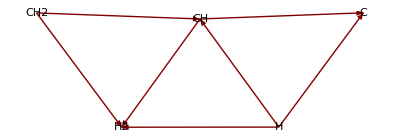

```mathematica
GraphPlot[Flatten[umist[[1;;2,{3,4,6,7}]]/.{a_,b_,c_,d_}->{{a->c,b},{a->d,b},{b->c,a},{b->d,a}},1],DirectedEdges->{True,"ArrowheadsSize"->Small},EdgeLabeling->None,VertexLabeling->True,MultiedgeStyle->None]
```

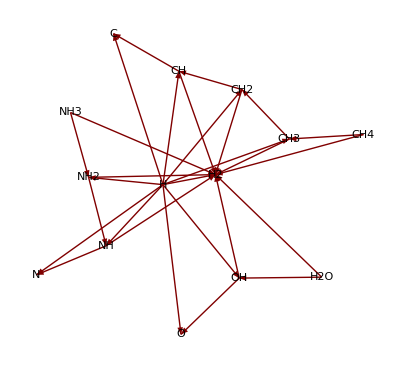

```mathematica
GraphPlot[Flatten[umist[[1;;10,{3,4,6,7}]]/.{a_,b_,c_,d_}->{{a->c,b},{a->d,b},{b->c,a},{b->d,a}},1],DirectedEdges->{True,"ArrowheadsSize"->Small},EdgeLabeling->None,VertexLabeling->True,MultiedgeStyle->None]
```

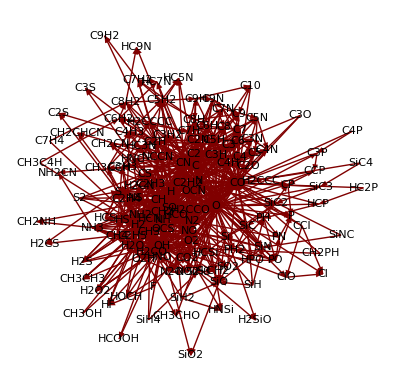

```mathematica
GraphPlot[Flatten[umist[[1;;500,{3,4,6,7}]]/.{a_,b_,c_,d_}->{{a->c,b},{a->d,b},{b->c,a},{b->d,a}},1],DirectedEdges->{True,"ArrowheadsSize"->Small},EdgeLabeling->None,VertexLabeling->True,MultiedgeStyle->None]
```

Some fancy graph theoretical tools in action:

```mathematica
<<Combinatorica`
Needs["GraphUtilities`"]
```

```mathematica
all=umist[[All,{3,4,6,7}]];
fullU=Flatten[all/.{a_,b_,c_,d_}->{a->c,a->d,b->c,b->d},1];
fullUc=ToCombinatoricaGraph@fullU;
```

```mathematica
TableForm[Transpose[{VertexList@fullU,InDegree@fullUc,OutDegree@fullUc}],TableHeadings->{None,{"Name","Formation","Destruction"}}]
```

Name | Formation | Destruction
H | 2158 | 228
C | 430 | 386
H2 | 1448 | 272
CH | 178 | 182
CH2 | 124 | 184
N | 270 | 298
NH | 140 | 136
CH3 | 278 | 112
NH2 | 86 | 120
CH4 | 158 | 236
O | 430 | 452
OH | 310 | 200
NH3 | 36 | 226
H2O | 278 | 208
C2 | 224 | 98
C2H | 128 | 148
C2H2 | 192 | 190
CN | 340 | 118
HCN | 172 | 146
C2H3 | 38 | 96
CO | 714 | 106
H2CN | 6 | 8
HCO | 118 | 170
NO | 154 | 166
H2CO | 114 | 164
HNO | 18 | 44
O2 | 154 | 186
O2H | 22 | 36
S | 204 | 154
HS | 86 | 42
H2O2 | 12 | 12
H2S | 34 | 176
OCN | 22 | 28
H2CCO | 10 | 22
CO2 | 84 | 80
N2 | 172 | 34
N2O | 20 | 40
NO2 | 14 | 36
NS | 16 | 32
SO | 52 | 52
NCCN | 24 | 40
OCS | 18 | 78
S2 | 10 | 18
HF | 8 | 12
F | 14 | 6
HNC | 32 | 66
C3 | 78 | 20
C3H | 38 | 66
C3H2 | 14 | 70
C2N | 22 | 20
C3H3 | 18 | 84
C2H4 | 62 | 178
C2O | 10 | 26
SiC | 12 | 32
SiH | 10 | 32
CH3CCH | 14 | 90
C2H5 | 30 | 40
HCSi | 8 | 18
SiH2 | 4 | 28
SiCH2 | 10 | 18
SiH3 | 14 | 22
CP | 20 | 16
PH | 30 | 16
CS | 88 | 32
C4 | 36 | 30
C4H | 28 | 76
H2CCC | 6 | 72
H2CCCC | 18 | 112
HC3N | 48 | 62
CH2CN | 8 | 10
C4H3 | 8 | 26
HPO | 4 | 18
C5 | 28 | 22
C3N | 28 | 20
C5H | 20 | 66
C3O | 8 | 26
C5H2 | 12 | 70
C6 | 30 | 24
C6H | 24 | 58
C6H2 | 16 | 56
CH3C4H | 2 | 24
SO2 | 18 | 32
C7 | 28 | 22
C5N | 22 | 16
C7H | 20 | 42
C8 | 32 | 24
C8H | 26 | 28
C7H2 | 10 | 48
C8H2 | 12 | 30
C7H4 | 2 | 18
C9 | 20 | 22
C7N | 18 | 16
C9H | 14 | 26
C10 | 2 | 16
C9N | 8 | 18
CH2NH | 4 | 14
CH3OH | 22 | 106
SiN | 18 | 14
HNSi | 6 | 14
PN | 12 | 12
Si | 88 | 102
P | 60 | 26
HCS | 4 | 18
PO | 12 | 14
C4N | 6 | 10
HC5N | 14 | 26
HC7N | 12 | 20
HOCH | 2 | 2
H2CS | 8 | 18
CH3CHO | 12 | 50
SiO | 44 | 24
H2SiO | 4 | 14
SiH4 | 4 | 38
PH2 | 10 | 14
HCP | 8 | 18
CH2PH | 2 | 16
Cl | 30 | 8
CCl | 2 | 12
ClO | 2 | 10
SiNC | 2 | 12
SiC2 | 12 | 14
CCP | 18 | 18
HC2P | 8 | 18
SiC3 | 10 | 12
C3P | 8 | 14
SiC4 | 2 | 10
C4P | 2 | 16
CH3CH3 | 22 | 78
HCOOH | 14 | 16
SiO2 | 4 | 6
NH2CN | 4 | 6
C2S | 12 | 26
C3S | 8 | 20
C9H2 | 8 | 22
CH2CHCN | 6 | 32
HC9N | 6 | 16
SiC2H2 | 4 | 14
He | 260 | 6
H2+ | 16 | 108
HeH+ | 6 | 6
C+ | 74 | 434
CH+ | 90 | 112
H+ | 32 | 378
CH2+ | 108 | 62
CH3+ | 106 | 176
CH4+ | 20 | 56
CH5+ | 24 | 76
H- | 8 | 68
OH- | 6 | 14
C2+ | 52 | 62
CN- | 12 | 6
C2H2+ | 100 | 190
C2H3+ | 92 | 156
C2H4+ | 68 | 120
CO+ | 72 | 76
NH2+ | 58 | 80
C2H5+ | 54 | 34
Si+ | 94 | 84
SiH+ | 30 | 20
HCO+ | 236 | 260
CH3CH3+ | 12 | 26
NO+ | 118 | 10
SiH2+ | 22 | 16
H3CO+ | 78 | 28
SiH3+ | 22 | 18
S+ | 90 | 94
HS+ | 54 | 48
H2S+ | 56 | 40
H3S+ | 50 | 16
C3+ | 40 | 28
C3H+ | 62 | 70
C3H2+ | 64 | 94
C3H3+ | 40 | 66
CH3CCH+ | 30 | 26
H2C3H+ | 52 | 66
SiC+ | 24 | 8
CH2CN+ | 16 | 4
CH3CN | 6 | 50
HCSi+ | 28 | 6
SiN+ | 14 | 4
SiCH2+ | 32 | 20
SiCH3 | 2 | 20
C3H6+ | 4 | 4
C3H7+ | 4 | 6
CO2+ | 10 | 34
HN2+ | 26 | 52
CS+ | 46 | 20
NO2+ | 8 | 6
SiOH+ | 28 | 6
C4+ | 30 | 16
C4H+ | 42 | 46
C4H2+ | 64 | 76
HCN+ | 46 | 58
C2N2+ | 6 | 18
HC3NH+ | 44 | 12
SiC2+ | 20 | 8
SiC2H | 4 | 18
SiC2H+ | 30 | 10
SiS+ | 10 | 8
C5+ | 24 | 24
C5H+ | 42 | 14
SO+ | 34 | 20
SO2+ | 8 | 12
C5H3+ | 54 | 14
CH3C3N | 2 | 16
SiC3+ | 20 | 4
SiC3H | 2 | 14
C6+ | 28 | 18
C6H+ | 30 | 8
C6H5+ | 20 | 10
C6H6+ | 2 | 2
C7+ | 24 | 8
C7H+ | 34 | 12
C7H3+ | 46 | 12
CH3C5N | 2 | 14
C8+ | 24 | 6
C8H+ | 30 | 6
C9+ | 18 | 6
C9H+ | 28 | 12
CH3C7N | 2 | 14
H3+ | 10 | 338
He+ | 2 | 572
NH+ | 32 | 86
N+ | 20 | 112
OH+ | 38 | 104
O+ | 42 | 110
O- | 4 | 28
NH3+ | 110 | 48
H2O+ | 52 | 104
NH4+ | 122 | 22
H3O+ | 96 | 146
HF+ | 2 | 6
F+ | 2 | 4
H2F+ | 4 | 2
C2H+ | 84 | 70
CN+ | 28 | 66
HCNH+ | 118 | 48
HOC+ | 6 | 6
N2+ | 14 | 74
HNO+ | 22 | 46
O2H+ | 8 | 48
SiH5+ | 8 | 10
SiH4+ | 4 | 12
HCl+ | 6 | 4
Cl+ | 10 | 6
H2Cl+ | 6 | 8
CH3CNH+ | 30 | 4
CH3CN+ | 14 | 8
HCP+ | 12 | 10
CP+ | 10 | 6
SiNH2+ | 12 | 8
HNSi+ | 8 | 10
PCH2+ | 16 | 4
HCO2+ | 30 | 22
HCS+ | 42 | 14
SiO+ | 18 | 32
HC3N+ | 16 | 32
C3N+ | 10 | 4
NCCNH+ | 14 | 14
HC3O+ | 24 | 2
C3O+ | 6 | 8
H4C3N+ | 10 | 6
C2H3CN+ | 4 | 4
HC2S+ | 18 | 6
C2S+ | 8 | 6
C5H2+ | 50 | 48
C4N+ | 4 | 20
H2C4N+ | 4 | 4
HC4N+ | 4 | 4
HSO2+ | 6 | 10
CH3C3N+ | 2 | 4
CH3C3NH+ | 10 | 6
C6H2+ | 48 | 40
HC5N+ | 14 | 6
C5N+ | 2 | 4
H2C5N+ | 10 | 4
C7H2+ | 46 | 26
C8H2+ | 46 | 12
HC7N+ | 12 | 6
C7N+ | 4 | 4
H2C7N+ | 8 | 4
C9H2+ | 44 | 10
HC9N+ | 12 | 6
C9N+ | 4 | 4
H2C9N+ | 8 | 4
Na+ | 52 | 8
Na | 8 | 52
Mg+ | 48 | 10
Mg | 10 | 48
H2CO+ | 68 | 60
PH+ | 16 | 38
H2NO+ | 4 | 4
PH2+ | 10 | 26
CH3OH2+ | 26 | 22
PH3+ | 8 | 12
HCl | 8 | 18
C2NH+ | 14 | 2
HC2O+ | 16 | 8
CH3CO+ | 28 | 4
NH2CNH+ | 4 | 4
SiCH3+ | 12 | 8
SiCH4+ | 12 | 6
HN2O+ | 10 | 4
CH3CHOH+ | 24 | 10
HPN+ | 6 | 6
H2CS+ | 14 | 6
PCH4+ | 12 | 6
C2H5OH | 6 | 36
CH3OCH4+ | 10 | 4
CH3OCH3 | 2 | 22
HNS+ | 6 | 2
H3CS+ | 16 | 4
H3SiO+ | 10 | 4
HPO+ | 16 | 10
H2PO+ | 14 | 4
HSO+ | 6 | 2
C4H3+ | 52 | 46
C4H4+ | 10 | 8
SiC2H2+ | 20 | 6
SiNCH+ | 10 | 6
SiC2H3+ | 14 | 6
HC2P+ | 14 | 4
Fe+ | 48 | 10
Fe | 10 | 48
PC2H2+ | 12 | 6
CH3COCH3 | 2 | 42
C3H5+ | 32 | 18
CH3COCH4+ | 16 | 4
H5C2O2+ | 8 | 4
HCOOCH3 | 2 | 16
HOCS+ | 10 | 6
HSiO2+ | 4 | 4
HSiS+ | 6 | 12
SiS | 8 | 20
C5H5+ | 32 | 6
SiC3H+ | 20 | 6
HS2+ | 14 | 8
SiC3H2+ | 12 | 6
H2S2+ | 14 | 4
HS2 | 8 | 12
H3S2+ | 8 | 4
H2S2 | 2 | 12
PC3H+ | 8 | 6
HC3S+ | 20 | 4
C6H3+ | 48 | 10
SiC4H+ | 12 | 4
C6H7+ | 22 | 4
C6H6 | 2 | 26
PC4H+ | 8 | 8
HC4S+ | 12 | 6
C4S | 2 | 20
C7H5+ | 22 | 6
CH3C5NH+ | 6 | 6
C8H3+ | 38 | 10
C9H3+ | 40 | 8
CH3C7NH+ | 6 | 6
P+ | 28 | 34
O2+ | 48 | 70
PO+ | 24 | 2
C2N+ | 26 | 16
S2+ | 10 | 12
CCP+ | 12 | 4
H2NC+ | 14 | 6
CF+ | 2 | 2
CNC+ | 6 | 6
C- | 2 | 50
CCl+ | 4 | 6
SiNC+ | 16 | 4
C3S+ | 8 | 6
SiC4+ | 10 | 4
H3C5N+ | 8 | 4
H3C7N+ | 10 | 4
C10+ | 12 | 4
H3C9N+ | 8 | 4
CH2CO+ | 18 | 6
NS+ | 14 | 4
C4H5+ | 10 | 6
CH3C4H+ | 26 | 6
C7H4+ | 22 | 6
C9H4+ | 20 | 6
CH4N+ | 6 | 4
OCN+ | 8 | 2
H2CCl+ | 6 | 2
H2SiO+ | 6 | 4
PN+ | 2 | 6
OCS+ | 24 | 10
PCH3+ | 4 | 6
HCOOH2+ | 10 | 12
C6H4+ | 36 | 4
C8H4+ | 22 | 4
C2H7+ | 6 | 10
PNH2+ | 4 | 6
PNH3+ | 4 | 6
CH2NH2+ | 6 | 4
C2H5OH2+ | 8 | 8
HNCO+ | 2 | 2
N2O+ | 4 | 8
SiF+ | 2 | 2
C2O+ | 6 | 2
C4H7+ | 6 | 2
PC2H3+ | 4 | 6
CH3CS+ | 2 | 2
PC2H4+ | 2 | 6
CH3COCH3+ | 10 | 6
C4S+ | 6 | 6
CH3OH+ | 14 | 2
CH3CHO+ | 8 | 4
C2H5OH+ | 8 | 4
CH3OCH3+ | 8 | 4
COOCH4+ | 6 | 4
C4P+ | 2 | 4
ClO+ | 2 | 2
S- | 2 | 34
e- | 318 | 1022
HCOOH+ | 2 | 4
C3H2O+ | 2 | 4
H3C3O+ | 2 | 2
NCCNCH3+ | 2 | 2
C8H5+ | 2 | 4
C9H5+ | 2 | 4
PHOTON | 230 | 432
CRP | 0 | 22
CRPHOT | 0 | 312
M | 58 | 2

## Expressions

Required Reading

Everything is an Expression
Basic Objects

### Form of Expressions

Mathematica treats everything (all Input, all Output) as an expression. A Mathematica expression has the form expression f[x,y,…] with the Head f and the  elements x,y,...

A prototypical example of a Mathematica expression is f[x,y]. We might use this expression to describe the function f(x,y). The name of the function is f, its arguments are x and y. Here, f is the Head of the expression.

```mathematica
Head[f[x,y]]
```

f

The same is true for any other 'thing' you might type into Mathematica, even in less obvious cases

```mathematica
a+b
```

a+b

```mathematica
Head[a+b]
```

Plus

```mathematica
Head[a=b]
```

Symbol

```mathematica
Head[a*b]
```

Power

```mathematica
{1,2,3,4,5,6}
Head[%]
```

{1,2,3,4,5,6}

List

To see the full form of an expression use FullForm

```mathematica
FullForm[a+b+c+d+e+f]
```

Plus[Times[2,b],c,d,e,f]

```mathematica
FullForm[a x^2+b x+c]
```

Plus[c,Times[b,x],Times[b,Power[x,2]]]

```mathematica
FullForm[2+y^3-(x+y+z^2)^2]
```

Plus[2,Power[y,3],Times[-1,Power[Plus[x,y,Power[z,2]],2]]]

```mathematica
FullForm[{{1,2},{3,4}}]
```

List[List[1,2],List[3,4]]

The FullForm is a compound of more simple expressions. The simplest expressions are called atoms.

```mathematica
FullForm["Mathematica"]
```

"Mathematica"

If FullForm can not reveal a structure we reached atomic level. AtomQ[expr] tests whether an expressions is an atom.

```mathematica
AtomQ["Mathematica"]
```

True

```mathematica
Head["Mathematica"]
```

String

```mathematica
FullForm[x]
```

x

```mathematica
Head[x]
```

Symbol

```mathematica
FullForm[Integrate]
```

Integrate

```mathematica
Head[Integrate]
```

Symbol

Atomic objects are:

Symbol
String
Integer
Real
Rational
Complex

### Parts of Expressions

Required Reading

Parts of Expressions

Since List are just a special kind of expression you can use Part to also access parts of expressions

```mathematica
List[a,b,c,d,e,f,g ]
%[[2]]
```

{b,b,c,d,e,f,g}

b

```mathematica
Plus[a,b,c,d,e,f,g]
%[[4]]
```

2 b+c+d+e+f+g

e

```mathematica
a+b+c+d+e+f+g
%[[4]]
```

2 b+c+d+e+f+g

e

```mathematica
(a+b+c+d+e+f+g)[[-2]]
```

f

```mathematica
List[a,b,c,d,e,f,g ]
Length[%]
```

{b,b,c,d,e,f,g}

7

```mathematica
Plus[a,b,c,d,e,f,g]
Length[%]
```

2 b+c+d+e+f+g

6

The 0th part is the head

```mathematica
(a+b+c+d+e+f+g)[[0]]
```

Plus

```mathematica
(a*b*c*d*e*f*g)[[0]]
```

Times

```mathematica
{a,b,c,d,e,f,g}[[0]]
```

List

### Levels in Expressions

Required Reading:

Levels in Expressions

Compound expressions consists of nested expressions:

```mathematica
expr=a+b^c
```

b+b^c

```mathematica
FullForm[expr]
```

Plus[b,Power[b,c]]

```mathematica
Length[expr]
```

2

```mathematica
expr[[1]]
expr[[2]]
```

b

b^c

The 2nd element of expr is not yet atomic.

```mathematica
FullForm[%]
```

Power[b,c]

```mathematica
expr[[2]][[0]]
expr[[2]][[1]]
expr[[2]][[2]]
```

Power

b

c

The structure can be visualized with TreeForm

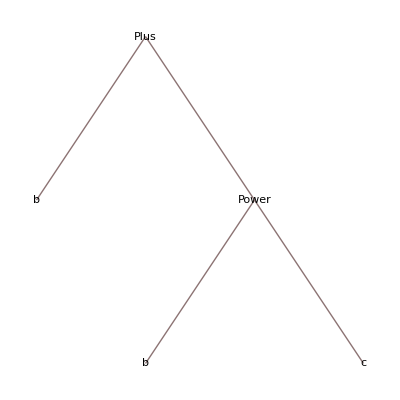

```mathematica
TreeForm[expr]
```

Like in lists you can search for parts of expressions, etc:

```mathematica
exp=TrigExpand[Sin[x]^3+Cos[x]^2+(Sin[x]Cos[x])/(Sin[x]+Cos[x])]
```

1/2+Cos[x]^2/2+(3 Sin[x])/4-3/4 Cos[x]^2 Sin[x]-Sin[x]^2/2+Sin[x]^3/4+(Cos[x] Sin[x])/(Cos[x]+Sin[x])

```mathematica
Position[exp,Sin[_]^2]
```

{{5,2}}

What doest the result mean? Position produces a list of positions where the pattern was found.

```mathematica
exp[[5]]
exp[[5]]//FullForm
```

-1/2 Sin[x]^2

Times[Rational[-1,2],Power[Sin[x],2]]

The FullForm shows the structure of the -1/2 Sin[x]^2term. Its second part is the squared sine.

```mathematica
exp[[5]][[2]]
exp[[5,2]]
```

Sin[x]^2

Sin[x]^2

Many other Mathematica commands accept patterns. We can, for example, count all sine squared terms with Count[list,pattern]. Try

```mathematica
Count[exp,Sin[_]^2]
```

0

What went wrong? Clearly, the pattern is correct, because we managed to pull out the Sin[]^2 position. Looking at Count shows that the full list of arguments looks like: Count[expr,pattern,levelspec]and gives the total number of subexpressions matching pattern that appear at the levels in expr specified by levelspec. The defaul level specification is {1} which means, only count through all level 1 elements. Looking at the TreeForm of exp shows ,that Sin[x]^2 sits at a lower level:

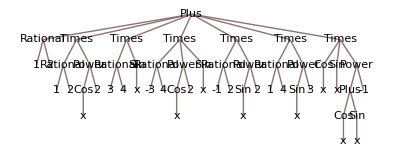

```mathematica
TreeForm[exp]
```

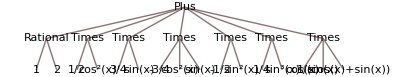

```mathematica
TreeForm[exp,2]
```

```mathematica
Count[exp,Sin[_]^2,1]
Count[exp,Sin[_]^2,2]
Count[exp,Sin[_]^2,3]
Count[exp,Sin[_]^2,Infinity]
```

0

1

1

1

Depth[expr]gives the total number of levels in an expressions.

```mathematica
Depth[exp]
```

6

Level[expr,lev]gives a list of the parts of expr at the levels specified by lev.

This gives a list of all parts of exp that occur down to level 2.

```mathematica
Level[exp,2]
```

{1/2,1/2,Cos[x]^2,Cos[x]^2/2,3/4,Sin[x],(3 Sin[x])/4,-3/4,Cos[x]^2,Sin[x],-3/4 Cos[x]^2 Sin[x],-1/2,Sin[x]^2,-1/2 Sin[x]^2,1/4,Sin[x]^3,Sin[x]^3/4,Cos[x],Sin[x],1/(Cos[x]+Sin[x]),(Cos[x] Sin[x])/(Cos[x]+Sin[x])}

Here are the parts specifically at level 2.

```mathematica
Level[exp,{2}]
```

{1/2,Cos[x]^2,3/4,Sin[x],-3/4,Cos[x]^2,Sin[x],-1/2,Sin[x]^2,1/4,Sin[x]^3,Cos[x],Sin[x],1/(Cos[x]+Sin[x])}

#### Excercises

What is the difference between the following two expressions

```mathematica
Count[exp,Sin[_]^2,3]
```

1

```mathematica
Count[exp,Sin[_]^2,{3}]
```

0

```mathematica
Clear[exp]
```

### Excercises

What does the Function LeafCount. Apply it to the expression exp from above.

Taken the expression exp from above, count the occurence of the rational 1/2.

Predict the results of the following Mathematica inputs, and compare each prediction with the actual Mathematica output. 
1)	2+3I
2)	Head[2+3I]
3)	2+0I
4)	Head[2+0I]
5)	FullForm[0]
6)	Infinity-Infinity
7)	Plus[Times[Plus[]],Times[]]

Analyze the following expression as Mathematica expression:

expr = ln(Sqrt[sin(x)] + E^(x + x^2)) cos^2(x)-ln(ln(ln(E^ⅇ+1)))

Find its depth. Examine the various levels. Where does ⅇ occur? Where x?

## Rules & Patterns

### Finding Expressions that Match a Pattern

Required Reading:

Finding Expressions That Match a Pattern

Pattern Overview	

Patterns for Some Common Types of Expression

Patterns are used throughout Mathematica to represent classes of expressions.
A simple example of a pattern is the expression f[x_]. This pattern represents the class of expressions with the form f[anything].

The main power of patterns comes from the fact that many operations in Mathematica can be done not only with single expressions, but also with patterns that represent whole classes of expressions.

You can use patterns in transformation rules to specify how classes of expressions should be transformed.

```mathematica
f[a]+f[b]/.f[x_]->x^2
```

2 b^2

```mathematica
Position[{f[a],g[b],f[c]},f[x_]]
```

{{1},{3}}

The basic object that appears in almost all Mathematica patterns is _ (traditionally called “blank” by Mathematica programmers). The fundamental rule is simply that _ stands for any expression. On most keyboards the _ underscore character appears as the shifted version of the - dash character.

Thus, for example, the pattern f[_] stands for any expression of the form f[anything]. The pattern f[x_] also stands for any expression of the form f[anything], but gives the name x to the expression anything, allowing you to refer to it on the right-hand side of a transformation rule.

f[n_] | f with any argument, named n
f[n_,m_] | f with two arguments, named n and m
x^n_ | x to any power, with the power named n
x_^n_ | any expression to any power
a_+b_ | a sum of two expressions
{a1_,a2_} | a list of two expressions
f[n_,n_] | f with two identical arguments

Many Mathematica functions accept patterns. For example:
Cases[{e_1,e_2,…},pattern]	gives a list of the e_i that match the pattern. 
Position[expr,pattern]		gives a list of the positions at which objects matching pattern appear in expr.

```mathematica
Cases[{1,1,f[a],2,3,y,f[8],9,f[10]},_Integer]
```

{1,1,2,3,9}

```mathematica
Cases[{3,4,x,x^2,x^3},x^_]
```

{x^2,x^3}

```mathematica
Count[{3,4,x,x^2,x^3},x^_]
```

2

```mathematica
Position[Table[Fibonacci[n],{n,1,10}],_?EvenQ]
```

{{3},{6},{9}}

The pattern x^_ does not implicitely pick x^1 or x^0. See the example below how to work around this.

You can use Cases[expr,lhs->rhs]to pick out the wanted elements and apply transformation rules to them:

```mathematica
Cases[{1,x,x^2,x^3,x^4,x^5},x^n_->n^2-1]
```

{3,8,15,24}

#### Excercise

What is the difference between _, __, ___?

You can specify to which level you want to search. Consider the following Mathematica expressions and predict their result. Check your predictions:
Cases[{3, 4, x, x^2, x^3}, _Integer]
Cases[{3, 4, x, x^2, x^3}, _Integer, 1]
Cases[{3, 4, x, x^2, x^3}, _Integer, 2]
Cases[{3, 4, x, x^2, x^3}, _Integer, {2}
Cases[{3, 4, x, x^2, x^3}, _Integer, Infinity]]

### Finding Expressions that Meet a Criterion

Required Reading:

Selecting Parts of Expressions with Functions

Select[expr,f] select the elements in expr for which the function f gives True

```mathematica
Select[{1,2,4,7,6,2},EvenQ]
```

{2,4,6,2}

Use a pure function to test each element:

```mathematica
Select[{1,2,4,7,6,2},#>2&]
```

{4,7,6}

#### Excercises

Create a list of 1000 random integers between 1 and 1 million and extract all that are dividable by 
a) 7
b) 3
c) 2

If you used Select for the above excercise, try to find a solution applying Cases.

Create as list of binary numbers from 1 to 1024 and filter ot the palindromic numbers, i.e. the numbers that are the same after bit reversal.

### Applying Transformation Rules

Required Reading:

Transformation Rules and Definitions

expr /. lhs -> rhs	apply a transformation rule to expr

/. is the short form of ReplaceAll

A Rule is represented by -> or →. lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs. The character -> can be entered as Esc -> Esc or ∖[Rule]. lhs->rhs evaluates rhs immediately.

```mathematica
x+y/.x->3
```

3+y

```mathematica
{a,b,c,d,e,f,g}/.a->1
```

{1,1,c,d,e,f,g}

```mathematica
{a,b,c,d,e,f,g}/.{a->1,b->2}
```

{1,1,c,d,e,f,g}

Functions such as Solve and NSolve return lists whose elements are lists of rules, each representing a solution.

```mathematica
Solve[x^3-5x^2+2x+8==0,x]
```

{{x→-1},{x→2},{x→4}}

When you apply these rules, you get a list of results, one corresponding to each solution.

```mathematica
x^2+6/.%
```

{7,10,22}

When you use expr/.rules, each rule is tried in turn on each part of expr. As soon as a rule applies, the appropriate transformation is made, and the resulting part is returned.

The rule for x^3 is tried first; if it does not apply, the rule for x^n_ is used.

```mathematica
{x^2,x^3,x^4}/.{x^3->u,x^n_->p[n]}
```

{p[2],u,p[4]}

The replacement expr/.rules tries each rule just once on each part of expr.

```mathematica
{x^2,y^3}/.{x->y,y->x}
```

{y^2,x^3}

```mathematica
x^2/.{x->(1+y),y->b}
```

(1+y)^2

```mathematica
x^2/.x->(1+y)/.y->b
```

(1+b)^2

Sometimes you may need to go on applying rules over and over again, until the expression you are working on no longer changes. You can do this using the repeated replacement operation expr//.rules (or ReplaceRepeated[expr,rules]).

```mathematica
x^2+y^6/.{x->2+a,a->3}
```

(2+b)^2+y^6

```mathematica
x^2+y^6//.{x->2+a,a->3}
```

25+y^6

You can use rules to define certain restructuring rules on expressions:

```mathematica
log[a b c d]//.log[x_ y_]->log[x]+log[y]
```

log[b^2]+log[c]+log[d]

If you had used /. the rule would have been applied only once

```mathematica
log[a b c d]//.log[x_ y_]->log[x]+log[y]
```

log[b^2]+log[c]+log[d]

Be carefule not to create an infinite loop by doing repeated replacements.

```mathematica
x//.x->x+1
```

ReplaceRepeated::rrlim: Exiting after x scanned 65536 times.

65536+x

It is also possible to use Replace[expr,rules,levspec]to apply rules to parts ofexpr on levels specified by levspec.

```mathematica
Replace[{{x,y,y,z,x},{y,x,{x,y,y},z},x,y},x->X,1]
Replace[{{x,y,y,z,x},{y,x,{x,y,y},z},x,y},x->X,2]
Replace[{{x,y,y,z,x},{y,x,{x,y,y},z},x,y},x->X,3]
Replace[{{x,y,y,z,x},{y,x,{x,y,y},z},x,y},x->X,{2}]
```

{{x,y,y,z,x},{y,x,{x,y,y},z},X,y}

{{X,y,y,z,X},{y,X,{x,y,y},z},X,y}

{{X,y,y,z,X},{y,X,{X,y,y},z},X,y}

{{X,y,y,z,X},{y,X,{x,y,y},z},x,y}

#### Excercises

Define a rule which transforms a pair of Cartesian coordinates {x_,y_} into a Cartesian tripple with z=0.

Define a rule which transforms a pair of Cartesian coordinates {x_, y_} into polar form {r, θ} using a quadrant - sensitive form of ArcTan that accepts two arguments.  Test your function on a list of points, such as {{1, 2}, {-2, -3}, {0, 1}, {-3, 0}}?  Define another rule which performs the inverse transformation and test.

Define a rule which expresses exponential functions in terms of hyperbolic sine and cosine functions (note: Exp[x]=Sinh[x] +Cosh[x]).   Test your rule on the expression x Exp[-y^2].

Perform the change of variables x→Sin[θ] on the following expression: (x ⅆx)/(1-x^2).  Be sure to make the corresponding replacement of the differential in the numerator also, and simplify the result.

Create rules to simplify Log[a x] and Log [a^n].

Stirling's approximation suggests Log[n!]≈n Log[n]-n.  Use this approximation, together with rules for logarithms, to evaluate  Log[(n!)/(m!(n-m)!)].

Gauss's version of the lensmaker's formula reads 1/s_i+1/s_o==1/f.  Use the substitutions x_i=s_i-f,x_o=s_o-f and solve for f to derive Newton's version x_i x_o==f^2.

### Delayed rules

RuleDelayed, or lhs:>rhs or lhs:>rhs represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used.

-> evaluates when it is first entered; :> when it is used:

```mathematica
x->RandomReal[]
```

x→0.861217

```mathematica
x:>RandomReal[]
```

x:>RandomReal[]

```mathematica
{x,x,x}/.x:>RandomReal[]
```

{0.0836761,0.854795,0.635584}

```mathematica
{x,x,x}/.x->RandomReal[]
```

{0.329753,0.329753,0.329753}

Application example:Increment n each time x is replaced:

```mathematica
n=1;{x,x,a,b,x,x,c,d}/.x:>n++
```

{1,2,b,b,3,4,c,d}

#### Excercise

Create a list of integers from 1 to 20 and replace all even numbers with the next smaller integer.

What happens if the rule based sorting is applied to lists with one ore more identical elements? Can you extend the command to handle this case as well?

### Patterns Involving Alternatives

patt_1|patt_2|…		a pattern that can have one of several forms

```mathematica
{a,b,c,d}/.(a|b)->p
```

{p,p,c,d}

```mathematica
{1,x,x^2,x^3,y^2}/.(x|x^_)->q
```

{1,q,q,q,y^2}

Pick out integers or reals:

```mathematica
Cases[{5.6,5/6,5,6,x},_Integer|_Real]
```

{5.6,5,6}

### Putting Constraints and Tests on Patterns

Required Reading:

Putting Constraints on Patterns

p?test		is a pattern object that stands for any expression which matches p, and on which the 			application of test gives True.

```mathematica
Cases[{1,2,3.5,x,y,4},_?NumberQ]
```

{1,2,3.5,4}

To test an if a pattern matches an expression you can use MatchQ[expr,form]. E.g. Test if an expression is an integer:

```mathematica
MatchQ[12345,_Integer]
```

True

```mathematica
MatchQ["Mathematica",_String]
```

True

Mathematica provides a general mechanism for specifying constraints on patterns. All you need do is to put /;condition at the end of a pattern to signify that it applies only when the specified condition is True. You can read the operator /; as "slash-semi", "whenever" or "provided that".

```mathematica
{6,-7,3,2,-1,-2}/.x_/;x<0->w
```

{6,w,3,2,w,w}

```mathematica
Cases[{3,-4,5,-2},x_/;x<0]
```

{-4,-2}

The rule applies to all elements of the list that are numbers.

```mathematica
{2.3,4,7/8,a,b}/.(x_/;NumberQ[x])->x^2
```

{5.29,16,49/64,b,b}

```mathematica
Cases[{1,0,2,0,3},Except[0]]
```

{1,2,3}

```mathematica
Cases[{a,b,0,1,2,x,y},Except[_Integer]]
```

{b,b,x,y}

#### Example application: maxima problem

Here is the so-called maxima problem (proposed by R. Gaylord). Given a list of positive integers, make a new list of those numbers in the original list (in their original order) that are greater than all of their predecessors. Thus, for example, starting with the list {3, 2, 8, 1, 10}, Maxima[{3, 2, 8, 1, 10}] should give the result {3, 8, 10}.

```mathematica
maxima[l_List] := l //. {a___, x_, y_, c___} :> ({a, x, c} /; y <= x)
```

```mathematica
maxima[{1, 2, 3, 2, 1, 5, 3, 2, 8, 0, 0, 1, 23}]
```

{1,2,3,5,8,23}

#### Example application: Sorting

A brief outlook to rule based programming: We will use rules and conditions to implement a sort command that works on lists of real numbers.

```mathematica
r=RandomSample[Range[1000],50]
```

{268,633,210,393,536,283,921,986,217,734,113,46,851,80,245,545,820,720,960,966,502,672,836,653,338,957,604,569,239,288,943,129,642,955,513,743,336,795,273,760,286,237,135,143,618,15,974,507,637,973}

```mathematica
r//.{a___,b_,c___,d_,e___}:>{a,d,c,b,e}/;d<b
```

{15,46,80,113,129,135,143,210,217,237,239,245,268,273,283,286,288,336,338,393,502,507,513,536,545,569,604,618,633,637,642,653,672,720,734,743,760,795,820,836,851,921,943,955,957,960,966,973,974,986}

#### Excercises

Create a list with the first 30 Fibonacci numbers and select the cases that are dividable by 7.

### An Example: Defining Your Own Integration Function

This section consists of the Mathematica tutorial: An Example: Defining Your Own Integration Function

Read the tutorial and consider the following questions:

The tutorial defines a custom integrate routine. To that end multiple definitions for the functions integrate are given to cover several integration rules. Study the setup of the integrate function.

What is the purpose of the following definition:

```mathematica
integrate[c_ y_,x_]:=c integrate[y,x]/;FreeQ[c,x]
```

Explain the syntax: /; FreeQ[c, x]

In the following definition:

```mathematica
integrate[x_^n_.,x_]:=x^(n+1)/(n+1)/;FreeQ[n,x]&&n!=-1
```

Explain the pattern n_.

Explain FreeQ[n, x] && n != -1

### String Patterns

Required Reading:

String Patterns Tutorial
String Patterns Guide
Working with String Patterns

A string in Mathematica is enclosed in quotes. Patterns are not part of a string, but of a StringExpression. 
s_1~~s_2~~… or StringExpression[s_1,s_2,…]represents a sequence of strings and symbolic string objects s_i.

A string expression representing the string "ab" followed by any single character:

```mathematica
"ab" ~~ _
```

ab~~_

This makes a replacement for each occurrence of the string pattern "ab"~~__:

```mathematica
StringReplace["abc abcb abdc","ab"~~_->"X"]
```

X Xb Xc

If consecutive elements in a string expression are strings, then they are automatically concatenated to one string. Here is an example of this situation.

```mathematica
StringExpression["1", 2]
```

1~~2

```mathematica
StringExpression["1", "2", 3]
```

12~~3

Let's look at all built-in functions having the name String… and having nonstring analog. Here is a list of these functions.

```mathematica
Select[Names["String*"], MemberQ[Names["*"], StringDrop[#, 6]]&]
```

{StringBreak,StringByteCount,StringCases,StringCount,StringDrop,StringExpression,StringFormat,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPosition,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringSkeleton,StringSplit,StringTake}

To find out if a given string matches a given pattern, the function StringMatchQ can be used.

```mathematica
StringMatchQ["123456789", "1" ~~ _ ~~ "9"]
```

False

```mathematica
StringMatchQ["123456789", "1" ~~ __ ~~ "9"]
```

True

Here are some possibilities to match any string of length two or larger.

```mathematica
StringMatchQ["abc", StringExpression[__]]
```

True

```mathematica
StringMatchQ["abc", StringExpression[_ ..]]
```

True

Here we used the Repeated (..)operator. p.. or Repeated[p]is a pattern object which represents a sequence of one or more expressions, each matching p.

If you want to check that a string is free of "a" use StringFreeQ:

```mathematica
StringFreeQ["abcd","a"]
```

False

Find the starting and ending positions at which XYZ occurs in a string use StringPosition["string","sub"]

```mathematica
StringPosition["abXYZaaabXYZaaaaXYZXYZ","XYZ"]
```

{{3,5},{10,12},{17,19},{20,22}}

The next input determines the string position of a substring that begins with the substring "1" and is followed by at least one more character.

```mathematica
StringPosition["12345678987654321", "12" ~~ __]
```

{{1,17}}

The last call to StringPosition returned the whole string—the longest possible match. To obtain the shortest possible match, we can use the function ShortestMatch.

```mathematica
StringPosition["12345678987654321", ShortestMatch["12" ~~ __]]
```

{{1,3}}

```mathematica
StringReplace["123456789", x:__:> "X"]
```

X

The above result again was the longest possible match. All possible matches are given by StringReplaceList

```mathematica
StringReplaceList["123456789", x:__:> "X"]
```

{X,X9,X89,X789,X6789,X56789,X456789,X3456789,X23456789,1X,1X9,1X89,1X789,1X6789,1X56789,1X456789,1X3456789,12X,12X9,12X89,12X789,12X6789,12X56789,12X456789,123X,123X9,123X89,123X789,123X6789,123X56789,1234X,1234X9,1234X89,1234X789,1234X6789,12345X,12345X9,12345X89,12345X789,123456X,123456X9,123456X89,1234567X,1234567X9,12345678X}

### Regular Expressions

Required Reading

Regular Expressions

You may sometimes find it convenient to specify string patterns using regular expression notation. You can do this in Mathematica with RegularExpression objects.  RegularExpression["regex"]represents the generalized regular expression specified by the string "regex".

Find words involving the characters a, b, c, d, e:

```mathematica
StringCases["adefgh12c34",RegularExpression["[a-e]+"]]
```

{ade,c}

Equivalent form using string patterns :

```mathematica
StringCases["adefgh12c34",CharacterRange["a","e"]..]
```

{ade,c}

Decide whether the string consists of words and whitespace:

```mathematica
StringMatchQ["abcd\nefgh\n1234",RegularExpression["(\\w|\\s)*"]]
```

True

Equivalent form using string patterns:

```mathematica
StringMatchQ["abcd\nefgh\n1234",(WordCharacter|Whitespace)...]
```

True

Numbered subpatterns:

```mathematica
StringCases["a1b6a3b3a3c3a8b8",RegularExpression["(a(\\d))b\\2"]->{"$0","$1","$2"}]
```

{{a3b3,a3,3},{a8b8,a8,8}}

#### Example: Highligh Patterns

This defines a 1000-base random DNA string.

```mathematica
SeedRandom[1234];dna=StringJoin[Table[{"a","c","g","t"}[[RandomInteger[{1,4}]]],{1000}]]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

This highlights parts of the DNA that match a certain pattern.

```mathematica
StringReplace[dna,x:("ag"~~_~~_~~"t"~~_~~"ca"):>"\!\(\*StyleBox[\""<>x<>"\",FontColor->RGBColor[1,0,0],FontSize->18,FontWeight->\"Bold\"]\)"]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

Here is the same result using a regular expression.

```mathematica
StringReplace[dna,RegularExpression["ag..t.ca"]:>"\!\(\*StyleBox[\"$0\",FontColor->RGBColor[1,0,0],FontSize->18,FontWeight->\"Bold\"]\)"]
```

tgaacggccgggaactaaaagacacagaccgcttctagttgacataccgacgaccgacaggttcaatgtgggtaatcgcgaagttgtgctcaatctgccgcgttaaagttgtagatgacaaccaagtacatgtccgacccaagtcgattcttagcggagtatatggcagtgtaagagcccgactgggtccctggttgagctcgtgcgcattgtattatcatttccggggtttcctaaggagagagtccgtacacctcagctttaaggagaaacactattctgcgccatctgcaacacatgagtctgttagcactccgaagagcgcttgagccagggaatgagcttcgctacctccgctgtaagtgcccctctctgcctctttccaacctccaatgcatgttgtcgccgttagccagtggtcggacagtctgaaatgttagcacgtagaaactctacccattacggccatttagtttaatgtcaacaatgtagctgccggaatcggattaacactcgcgaaacccataggtatgcccaccactgctctaggcagtgaacgagggttcacgactgtagatctctgatagcctcaaccccgtaaactggcatgatcccgatgctgctcgcgtagttgtgactattttaaactaggacttgtcccataaacatccccgcctcataagtgagacatcagcatgagtgacgtaacagattgattttgggcgcatctgaggcagcggcttaattcgtgcctcattcctaagaagacggggtattaattagaagcaatagcgctttgccgagccatctcgattgccagtccctcacatttatcgaggtgctgaagctgtggagggatgacactgtggctcctttgcaatcctcggacttagatcacactagccgctgcggtcgttcgtgagcgaccccgctcagtcgtagcccacgggaattgtcagcttaaagaaaaccgtgatctgtaaccaccggcgtctactcg

### Excercise

Create a list of 100 random integers between 1 and 1000 and extract all that are dividable by 
a) 7 or 5
b) neither 3 or 2
c) 2, 3 and 5

Create a list of 100 random integers between 1 and 10. Extract all elements except 5's.

Create your own symbolic sum function, including the common sum rules:

∑=∑_(i=1)^n 
∑(a_i+b_i) = ∑a_i+∑b_i
∑c a_i= c∑a_i
∑c= c n 
∑_(i=1)^m a_i+∑_(i=m+1)^n a_i=∑_(i=1)^n a_i, 1<m<n

Extend your sum function to include index shifts

∑_(i=1)^n a_i=∑_(i=x)^(n+x) a_(i-x)

Extend your sum function to include the special case

∑_(i=1)^n i=(n(n+1))/2

Can your sum function handle multiple sums:
∑_(j=1)^m ∑_(i=1)^n a_i b_j

Program solutions to the following problems; base the programs on pattern matching and the use of replacement rules. 
a) Given a list of elements (some of which may appear more than once), construct a list containing all (different) permutations of the elements. 
b) Given a list of the form {integer, nZeros}, for example, {23, 0, 0, 0, 0, 0}, construct all lists of integers a_i(i=1,…,n+1) (i.e., of the same length as the original list) with ∑_(i=1)^(n+1) a_i="integer" (i.e., which have the same sum as the original list). Put the a_i in increasing order: a_i≤a_(i+1),(i=1,…,n-1).

## Assignments

Required Reading:

Assignments
Making Definitions for Indexed Objects
Making Definitions for Functions
Immediate and Delayed Definitions
Special Forms of Assignment

### Set (=)

```mathematica
?=
```

RowBox[{StyleBox["lhs", "TI"], "=", StyleBox["rhs", "TI"]}] evaluates StyleBox["rhs", "TI"] and assigns the result to be the value of StyleBox["lhs", "TI"]. From then on, StyleBox["lhs", "TI"] is replaced by StyleBox["rhs", "TI"] whenever it appears. 
RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["l", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["l", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "=", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}] evaluates the SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]], and assigns the results to be the values of the corresponding SubscriptBox[StyleBox["l", "TI"], StyleBox["i", "TI"]].

In its simplest usage, Set assigns a value to a variable:

```mathematica
a=1
b=2
a+b^3
a
Set[a,2];
a
Clear[a,b]; (* clear variables *)
```

1

2

9

1

2

The left hand side is not restricted to single characters:

```mathematica
VolumeOfUnitSphere=(4 π)/3 (* use meaningful variable names *)
Clear[VolumeOfUnitSphere]
```

(4 π)/3

One can also asign lists to a variable:

```mathematica
a={1,2,3,4,5,6,7,8};
a[[3]]         (* get the third element of a *)
{a,b,c,d}={1,2,3,4};  (* assign multiple values *)
c
{a,b,c,d}={a,c,b,d}; (* swap values *)
c
Clear[a,b,c,d];
```

3

3

2

Generally, anything can be assigned to anything:

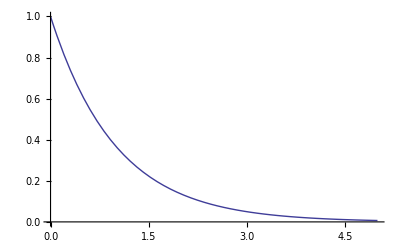
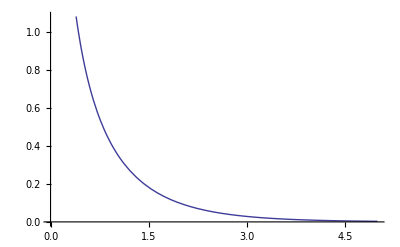

```mathematica
f=Plot[Exp[-t],{t,0,5}];
g=Plot[Exp[-t]/(√t),{t,0,5}];
f g
Clear[f,g]
```

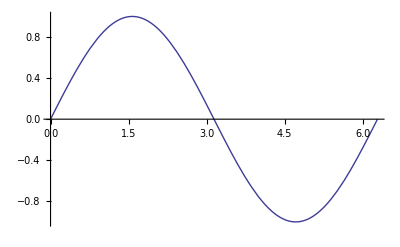

```mathematica
a=Plot;
a[Sin[x],{x,0,2 Pi}]
Clear[a];
```

```mathematica
t=TableForm[{{1,2,3,4,5,6,7,8,9,0},{a,b,c,d,e,f,g,h,i,j}},TableHeadings->Automatic];
t
Clear[t];
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 0
2 | a | b | c | d | e | f | g | h | i | j

Set is an immediate assignment. Say, we assign the value 2 to the symbol a (a=2). Now, whenever Mathematica meets the symbol a it immediately replaces it with its assigned value (2 in this case). Only then a calculation continues.
Example:

```mathematica
(a+b)^2
Integrate[x^2,{x,a,b}]
a=2;b=3;
(a+b)^2
Integrate[x^2,{x,a,b}]
Clear[a,b];
```

(a+b)^2

-a^3/3+b^3/3

25

19/3

### SetDelayed (:=)

```mathematica
?:=
```

RowBox[{StyleBox["lhs", "TI"], ":=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"]. StyleBox["rhs", "TI"] is maintained in an unevaluated form. When StyleBox["lhs", "TI"] appears, it is replaced by StyleBox["rhs", "TI"], evaluated afresh each time.

On a first glance SetDelayed works like Set:

```mathematica
a:=1
b:=2
a+b^3
a
Set[a,2];
a
Clear[a,b]; (* clear variables *)
```

9

1

2

The important difference is, that using a:= ... a remains enevaluated until it is used somewhere else. Why is this a difference? Take the following example, involving a random number generator:

```mathematica
?Random
```

RowBox[{"Random", "[", "]"}] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
RowBox[{"Random", "[", RowBox[{StyleBox["type", "TI"], ",", StyleBox["range", "TI"]}], "]"}] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range RowBox[{"{", RowBox[{StyleBox["min", "TI"], ",", StyleBox["max", "TI"]}], "}"}] explicitly; a range specification of StyleBox["max", "TI"] is equivalent to RowBox[{"{", RowBox[{"0", ",", StyleBox["max", "TI"]}], "}"}].

```mathematica
r=Random[] (* this first executes the right hand side, i.e. creates a random number, and then assigns the result to the left hand side *)
```

0.681162

```mathematica
{r,r,r}
```

{0.681162,0.681162,0.681162}

Now we use SetDelayed

```mathematica
r:=Random[] (* the right hand side remains unevaluated, note that there is no semi-colon to supress output *)
```

```mathematica
{r,r,r}
```

{0.854217,0.432088,0.897439}

Now, r is evaluated each time it is used! We will meet SetDelayed later, when we create functions.

One possible application is to perform a calculation on demand and cache the result:

```mathematica
pi2:=pi2=N[Pi^2,50]
```

```mathematica
pi2
```

9.8696044010893586188344909998761511353136994072408

```mathematica
Definition[pi2]
```

pi2=9.8696044010893586188344909998761511353136994072408

```mathematica
Clear[pi2]
```

### Example: Programming the Fibonacci sequence

Dynamic programming for the Fibonacci sequence:

```mathematica
Clear[fib]
```

```mathematica
fib[1]=fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

Note, that we chain f[x_]:=f[x]=.... this makes Mathematica remember f[x] which is especially important in iterative procedures. Sometimes, this might be unfeasible due to memory constraints. So far Mathematica does not know any Fibonacci number except 1.

```mathematica
Definition[fib]
```

fib[1]=1
 
fib[2]=1
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
fib[5]
```

5

After computing fib[5], Mathematica knows and remembers the intermediary steps.

```mathematica
fib[240]//AbsoluteTiming
```

{0.0156,64202014863723094126901777428873111802307548623680}

Since Mathematica now knows fib[240], the repeated call takes no time.

```mathematica
fib[240]//AbsoluteTiming
```

{0.,64202014863723094126901777428873111802307548623680}

The next iteration step is also almost instantaneous, since all 240 steps before are cached.

```mathematica
fib[241]//AbsoluteTiming
```

{0.,103881042195729914708510518382775401680142036775841}

If we omit the immediate Set in the definition, Mathematica is going to nest the fib[ ] functions which leads to very large computation times and possible kernel freezes( crashes).

```mathematica
Clear[fib]
```

```mathematica
fib1[1]=fib1[2]=1;
fib1[n_]:=fib1[n-1]+fib1[n-2]
```

```mathematica
fib[1]=fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
```

```mathematica
AbsoluteTiming[fib1[30]]
```

{2.3868,832040}

```mathematica
AbsoluteTiming[fib[30]]
```

{0.,832040}

```mathematica
Clear[fib,fib]
```

### Shortcuts

#### (Pre)Increment (++)

```mathematica
?Increment
```

RowBox[{StyleBox["x", "TI"], "++"}] increases the value of StyleBox["x", "TI"] by 1, returning the old value of StyleBox["x", "TI"].

```mathematica
k=1; k++
```

1

```mathematica
k
```

2

```mathematica
?PreIncrement
```

RowBox[{"++", StyleBox["x", "TI"]}] increases the value of StyleBox["x", "TI"] by 1, returning the new value of StyleBox["x", "TI"].

```mathematica
k=1; ++k
```

2

```mathematica
k
```

2

```mathematica
Clear[k]
```

#### (Pre)Decrement (--)

```mathematica
?Decrement
```

RowBox[{StyleBox["x", "TI"], "--"}] decreases the value of StyleBox["x", "TI"] by 1, returning the old value of StyleBox["x", "TI"].

```mathematica
k=1;k--
```

1

```mathematica
k
```

0

```mathematica
?PreDecrement
```

RowBox[{"--", StyleBox["x", "TI"]}] decreases the value of StyleBox["x", "TI"] by 1, returning the new value of StyleBox["x", "TI"].

```mathematica
k=1;--k
```

0

```mathematica
k
```

0

```mathematica
Clear[k]
```

#### AddTo, SubtractForm, TimesBy, DividedBy

```mathematica
?+=
```

RowBox[{StyleBox["x", "TI"], "+=", StyleBox["dx", "TI"]}] adds StyleBox["dx", "TI"] to StyleBox["x", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=1;k+=5
```

6

```mathematica
k
```

6

```mathematica
?-=
```

RowBox[{StyleBox["x", "TI"], "-=", StyleBox["dx", "TI"]}] subtracts StyleBox["dx", "TI"] from StyleBox["x", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=1;k-=5
```

-4

```mathematica
k
```

-4

```mathematica
?TimesBy
```

RowBox[{StyleBox["x", "TI"], "*=", StyleBox["c", "TI"]}] multiplies StyleBox["x", "TI"] by StyleBox["c", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=3;k*=5
```

15

```mathematica
k
```

15

```mathematica
?DivideBy
```

RowBox[{StyleBox["x", "TI"], "/=", StyleBox["c", "TI"]}] divides StyleBox["x", "TI"] by StyleBox["c", "TI"] and returns the new value of StyleBox["x", "TI"].

```mathematica
k=15;k/=3
```

5

```mathematica
k
```

5

```mathematica
Clear[k]
```

### Clearing Assignments

#### Unset

```mathematica
?=.
```

RowBox[{StyleBox["lhs", "TI"], "=."}] removes any rules defined for StyleBox["lhs", "TI"].

```mathematica
x=5;
x=.
x
```

x

#### Clear

```mathematica
?Clear
```

RowBox[{"Clear", "[", RowBox[{SubscriptBox[StyleBox["symbol", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["symbol", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for the SubscriptBox[StyleBox["symbol", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Clear", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for all symbols whose names match any of the string patterns SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

```mathematica
x=5
```

5

```mathematica
Clear[x]
```

#### ClearAll

```mathematica
?ClearAll
```

RowBox[{"ClearAll", "[", RowBox[{SubscriptBox[StyleBox["symb", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["symb", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] clears all values, definitions, attributes, messages and defaults associated with symbols. 
RowBox[{"ClearAll", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] clears all symbols whose names textually match any of the SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

We will omit ClearAll until we know a little more about functions and Attributes.

#### Remove

```mathematica
?Remove
```

RowBox[{"Remove", "[", RowBox[{SubscriptBox[StyleBox["symbol", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] removes symbols completely, so that their names are no longer recognized by StyleBox["Mathematica", FontSlant -> "Italic"]. 
RowBox[{"Remove", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] removes all symbols whose names match any of the string patterns SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

Later more on Remove